InitializationObjects

```mathematica
(*Retruns a Normal Vector for a line between two points*)
normalVector[{{x2_,y2_},{x1_,y1_}}]:=Module[{v},v={(-y2+y1),x2-x1} ; v/Norm[v]]
```

```mathematica
(*Retruns a Vector for a line between two points*)
vector[{{x2_,y2_},{x1_,y1_}}]:={x2-x1,y2-y1}
```

```mathematica
convexMinkowskiSum[robot_,obstacle_]:=Module[{robotLines,obstacleLines,robotVectors,obstacleVectors,mergedVectors,prev={0,0},result},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 07, 2019*)
(*Convert points of polygons as a list of two points representing a line*)
robotLines= Partition[Append[robot,First[robot]],2,1];
obstacleLines=Partition[Append[obstacle,First[obstacle]],2,1];
(*Calculate the Normal & Vector of lines(direction inwards for robot & outwards for Obstacles)*)
robotVectors= {(- normalVector[#]),-vector[#]}&/@robotLines; 
obstacleVectors={normalVector[#],vector[#]}&/@obstacleLines;
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
mergedVectors = Sort[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧}&/@Join [robotVectors,obstacleVectors],#1⟦1⟧<#2⟦1⟧&];
(*subtract the vector from the prev point to get the current point *)
result=RotateLeft[(Chop[prev=prev-#⟦2⟧])&/@mergedVectors,-1];
(*result=Append[result,First@result];*)
(#-centroidOfPolygon[result])&/@result
]

centroidOfPolygon[norm_]:= Module[{normArea,cX,cY},
normArea=(Total@Table[(norm⟦i⟧⟦1⟧*norm⟦i+1⟧⟦2⟧)-(norm⟦i+1⟧⟦1⟧*norm⟦i⟧⟦2⟧),{i,1,Length@norm-1,1}])/2;
{cX=(Total@Table[(norm⟦i⟧⟦1⟧+norm⟦i+1⟧⟦1⟧)((norm⟦i⟧⟦1⟧*norm⟦i+1⟧⟦2⟧)-(norm⟦i+1⟧⟦1⟧*norm⟦i⟧⟦2⟧)),{i,1,Length@norm-1,1}])/(6*normArea),
cY=(Total@Table[(norm⟦i⟧⟦2⟧+norm⟦i+1⟧⟦2⟧)((norm⟦i⟧⟦1⟧*norm⟦i+1⟧⟦2⟧)-(norm⟦i+1⟧⟦1⟧*norm⟦i⟧⟦2⟧)),{i,1,Length@norm-1,1}])/(6*normArea)}

]
```

```mathematica
convexMinkowskiSumRev1[robot_,obstacle_]:=Module[{vector,normalVectorAngle,makeLineList,prev={0,0}},

(*Retruns a Vector for a line between two points*)
vector[{{x2_,y2_},{x1_,y1_}}]:={x2-x1,y2-y1};

(*Retruns the angle of Normal Vector for a line between two points*)
normalVectorAngle[{{x2_,y2_},{x1_,y1_}}]:= 
ArcTan[(-y2+y1)/Norm[{(-y2+y1),x2-x1}],(x2-x1)]/Norm[{(-y2+y1),x2-x1}] ;

(*Returns Line Nested List of the Polygon*)
makeLineList[list_]:=Partition[Append[list,First[list]],2,1];

(*Returns the Minkowski Points*)
(prev=prev-#⟦2⟧)&/@(Sort[ {normalVectorAngle[#],vector[#]}&/@Join[makeLineList@(-robot),makeLineList@obstacle]])
]
```

```mathematica
findConvexHullCoordsConvexPolysAS[polyObstacle_,polyRobot_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦1,i⟧- polyRobot⟦1,j⟧,{i,1,Length[polyObstacle⟦1⟧]},{j,1,Length[polyRobot⟦1⟧]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
```

Demo code

```mathematica
Manipulate[Module[{robot,obstacle,robotLines,obstacleLines,robotNormal,obstacleNormal,robotArrows,obstacleArrows,robotAssignedNormal,obstacleAssignedNormal,mergedNormals,orderOfNormals,sortedArrows,sortedSides,rc,oc,sortedNormals,robotlabel,obstcalelabel,robotSubscript,obstacleSubscript,prev,minkowskiPoints},
(*robot =(r+# )&/@ CirclePoints[3];*)

(*Generate the robot & obstacle points*)
robot =pts⟦1;;m⟧;
obstacle =pts⟦6;;n+5⟧;

(*Centorids*)
rc=Mean@robot;
oc=Mean@obstacle;

(*Make a list having a set of two points a element *)
robotLines= Partition[Append[robot,First[robot]],2,1];
obstacleLines=Partition[Append[obstacle,First[obstacle]],2,1];

(*Get the Robot and Obstacle Normals*)
robotNormal = {(- normalVector[#]),-vector[#]}&/@robotLines; (* Robot inwards*)
obstacleNormal={normalVector[#],vector[#]}&/@obstacleLines;

(*Make Arrows on inside the polygons*)
robotArrows=Arrow[{rc,#⟦1⟧+rc}]&/@robotNormal; 
obstacleArrows = Arrow[{oc,#⟦1⟧+oc}]&/@obstacleNormal;	

(*Create Sub script*)
robotSubscript=Cases[Range[1,Length[robotNormal]],t:_:>Subscript[α, t]];
obstacleSubscript=Cases[Range[1,Length[obstacleNormal]],t:_:>Subscript[β, t]];

(*Assign the Edges of robot with α and obstacle as /[Beta]*)
robotAssignedNormal =AssociationThread[robotSubscript-> robotNormal];
obstacleAssignedNormal =AssociationThread[obstacleSubscript-> obstacleNormal];

(*Merge the Normals & add the angles in the value list*)
mergedNormals ={ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦1⟧,#⟦2⟧}&/@Join [robotAssignedNormal,obstacleAssignedNormal];

(*Sort the Normals based on angles*)
orderOfNormals = Sort[mergedNormals,#1⟦1⟧<#2⟦1⟧&];

(*Get the Minkowski Sum*)
prev={0,0};
(*minkowskiPoints=(Chop[prev=prev-#⟦3⟧])&/@Values@orderOfNormals;*)

minkowskiPoints=convexMinkowskiSum[robot,obstacle];
(*Make Arrows*) 
(*sortedNormals=sortNormals[robot,obstacle];*)
sortedArrows=Arrow[{{-3,0},{-3,0}+#⟦2⟧}]&/@Values[orderOfNormals];

(*Draw Text*)
robotlabel = Table[Text[Keys[robotAssignedNormal]⟦i⟧,(rc+1.2robotAssignedNormal⟦i⟧⟦1⟧)],{i,1,Length[robotAssignedNormal],1}];
obstcalelabel = Table[Text[Keys[obstacleAssignedNormal]⟦i⟧,(oc+1.2obstacleAssignedNormal⟦i⟧⟦1⟧)],{i,1,Length[obstacleAssignedNormal],1}];
sortedSides = Table[Text[Keys[orderOfNormals]⟦i⟧,{-3,0}+1.2orderOfNormals⟦i⟧⟦2⟧],{i,1,Length[orderOfNormals],1}];

Graphics[
{EdgeForm[Thin]
,{LightBlue, Polygon@robot}
,{LightRed, Polygon@obstacle}
,{LightGreen,Opacity[0.7], Polygon@minkowskiPoints}
,{obstacleArrows,robotArrows,robotlabel,obstcalelabel}
,{sortedArrows,sortedSides}
,{White,Disk[{-3,0},{0.5,0.5}]}
}]]
,{{pts,{{0.5,3.24},{0.41,2.25},{1.565,2.08}, 
  {1.465,3.54}, {0.735,3.59},{-2.4,2.19},{-2.048,3.30},{-3,4},{-3.95,3.30},{-3.5,2.13}}}
,{-5,-5},{5,5},Locator,Appearance->None}
,{{m,3,"Robot Edges"},3,5,1,Setter}
,{{n,4,"Obstacle Edges"},3,5,1,Setter}
]
```

#### Force polyomonio to stay convex (hide vertiex if non convex) make prettiere convert to Demo add description outline robot in blue, object in red, color code the lines on the Minkowski sum to match the original edges, maybe allow showing/hiding the normals

{{-1.57313,-0.115092},{-0.707107,-1.61509},{0.707107,-1.61509},{1.57313,-0.115092},{1.57313,1.29912},{0.158919,1.29912},{-1.57313,1.29912},{-1.57313,-0.115092}}

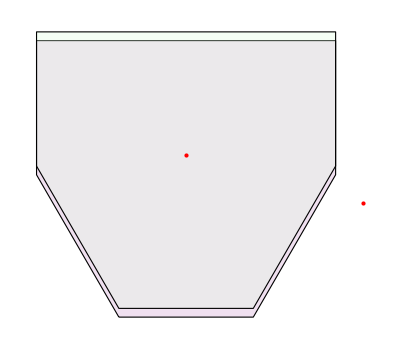

```mathematica
robot =N[CirclePoints[3]];
obstacle = N[CirclePoints[4]];
hull=findConvexHullCoordsConvexPolysAS[Polygon@obstacle,Polygon@robot];
norm=convexMinkowskiSum[robot,obstacle]
(*normArea=(Total@Table[(norm⟦i⟧⟦1⟧*norm⟦i+1⟧⟦2⟧)-(norm⟦i+1⟧⟦1⟧*norm⟦i⟧⟦2⟧),{i,1,Length@norm-1,1}])/2;
cX=(Total@Table[(norm⟦i⟧⟦1⟧+norm⟦i+1⟧⟦1⟧)((norm⟦i⟧⟦1⟧*norm⟦i+1⟧⟦2⟧)-(norm⟦i+1⟧⟦1⟧*norm⟦i⟧⟦2⟧)),{i,1,Length@norm-1,1}])/(6*normArea);
cY=(Total@Table[(norm⟦i⟧⟦2⟧+norm⟦i+1⟧⟦2⟧)((norm⟦i⟧⟦1⟧*norm⟦i+1⟧⟦2⟧)-(norm⟦i+1⟧⟦1⟧*norm⟦i⟧⟦2⟧)),{i,1,Length@norm-1,1}])/(6*normArea);
norm=(#-{cX,cY})&/@norm;*)
Graphics[{EdgeForm[Thin],{LightPurple,Polygon@hull},{Opacity[0.3],LightGreen,Polygon@norm(*,LightRed,Polygon@new*)},{Red,Point@{0,0},Point@{cX,cY}}}]
```

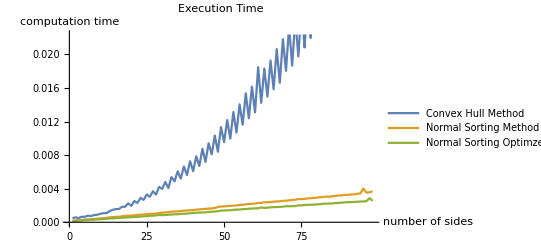

```mathematica
result=Table[robot =N[CirclePoints[i]];
obstacle =N[CirclePoints[i]];{AbsoluteTiming[findConvexHullCoordsConvexPolysAS[Polygon@obstacle,Polygon@robot]]⟦1⟧,
AbsoluteTiming[convexMinkowskiSum[robot,obstacle]]⟦1⟧,AbsoluteTiming[convexMinkowskiSumRev1[robot,obstacle]]⟦1⟧}
,{i,3,100,1}];
ListLinePlot[Transpose@result,PlotLegends->{"Convex Hull Method","Normal Sorting Method","Normal Sorting Optimzed"},AxesLabel->{"number of sides","computation time"},PlotLabel->"Execution Time"]
```